# MST

## Environment

```mathematica
$CharacterEncoding="UTF-8"
```

UTF-8

```mathematica
(*base="/home/kamano/"*)
```

```mathematica
base="/Users/amanokou/"
```

/Users/amanokou/

```mathematica
SetDirectory[base<>"gitsrc/ClusteringAdequation/test-data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/test-data

```mathematica
(*SetDirectory["/Users/kouamano/gitsrc/ClusteringAdequation/test-data"]*)
```

```mathematica
(*SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/test-data"]*)
```

## Program

```mathematica
(*Get["/Users/kouamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]*)
```

```mathematica
Get[base<>"/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]
```

```mathematica
(*Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Network_operations.txt"]*)
```

```mathematica
Get[base<>"gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]
```

```mathematica
(*Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt"]*)
```

```mathematica
Get[base<>"/gitsrc/MATH_SCRIPT/SCRIPTS/Version_ctrl.txt"]
```

## Example(1)

```mathematica
test={{1,2},{2,3},{3,1},{3,6},{5,2}}
```

{{1,2},{2,3},{3,1},{3,6},{5,2}}

Under Construction:

```mathematica
dmat=Outer[EuclideanDistance,test,test,1]
```

{{0,√2,√5,2 √5,4},{√2,0,√5,√10,√10},{√5,√5,0,5,√5},{2 √5,√10,5,0,2 √5},{4,√10,√5,2 √5,0}}

```mathematica
mstdm=MSTdmat[dmat]
```

{{{{1,2},√2},{{3,5},√5},{{2,3},√5},{{2,4},√10}},6}

```mathematica
mstd=mstD[dmat]
```

{{{},{{2,1},√2},{{5,3},√5},{{3,2},√5},{{4,2},√10}},{{1,2,3,4,5},{1,1,3,4,5},{1,1,3,4,3},{1,1,1,4,1},{1,1,1,1,1}}}

グループIDよりクラスターを生成

```mathematica
cls=Map[makeClusterByGr,mstd[[2]]]
```

{{{1},{2},{3},{4},{5}},{{1,2},{3},{4},{5}},{{1,2},{3,5},{4}},{{1,2,3,5},{4}},{{1,2,3,4,5}}}

MSTとクラスターよりエッジグループを生成

```mathematica
mstTotal=Map[Flatten[#]&,Drop[mstd[[1]],1],1]
```

{{2,1,√2},{5,3,√5},{3,2,√5},{4,2,√10}}

```mathematica
clBuilding=Map[makeEdgeGrFromCluster[mstTotal,#]&,cls]
```

{{{},{},{},{},{}},{{{2,1,√2}},{},{},{}},{{{2,1,√2}},{{5,3,√5}},{}},{{{2,1,√2},{5,3,√5},{3,2,√5}},{}},{{{2,1,√2},{5,3,√5},{3,2,√5},{4,2,√10}}}}

Max mst edge of each class on every K.

```mathematica
maxmstBuilding=Map[maxmstEdgeClusterd,clBuilding]
```

{{0,0,0,0,0},{√2,0,0,0},{√2,√5,0},{√5,0},{√10}}

maxMSTt

```mathematica
maxMSTt=Flatten[maxmstBuilding[[-1]]][[1]]
```

√10

CVI評価:

```mathematica
Table[mstPi2rkS[5][clBuilding[[n]]/.{}->{{0,0,0}},cls[[n]],maxMSTt],{n,5}]//N
```

{5.,4.32231,3.91696,3.26505,5.}

## Example(2)

```mathematica
test={{1,2},{2,3},{3,1},{3,6},{5,2}}
```

{{1,2},{2,3},{3,1},{3,6},{5,2}}

```mathematica
sn=50
```

50

```mathematica
test=Table[{RandomReal[],RandomReal[]},{sn}];
```

Under Construction:

```mathematica
dmat=Outer[EuclideanDistance,test,test,1];
```

```mathematica
mstdm=MSTdmat[dmat];
```

```mathematica
mstd=mstD[dmat];
```

グループIDよりクラスターを生成

```mathematica
cls=Map[makeClusterByGr,mstd[[2]]];
```

MSTとクラスターよりエッジグループを生成

```mathematica
mstTotal=Map[Flatten[#]&,Drop[mstd[[1]],1],1];
```

```mathematica
clBuilding=Map[makeEdgeGrFromCluster[mstTotal,#]&,cls];
```

Max mst edge of each class on every K.

```mathematica
maxmstBuilding=Map[maxmstEdgeClusterd,clBuilding];
```

maxMSTt

```mathematica
maxMSTt=Flatten[maxmstBuilding[[-1]]][[1]]
```

0.226309

CVI評価:

```mathematica
Table[mstPi2rkS[5][clBuilding[[n]]/.{}->{{0,0,0}},cls[[n]],maxMSTt],{n,sn}]//N
```

{50.,49.0625,48.1443,47.244,46.3445,45.4493,44.5873,43.7182,42.898,42.0719,41.2531,40.4267,39.6269,38.6557,37.9377,37.1657,36.4687,35.7425,35.0281,34.3193,33.6663,32.9823,32.3116,31.4698,30.7506,30.0197,29.184,28.6055,27.8184,26.8997,26.1226,25.3783,24.9016,23.9028,23.5088,22.3064,22.0549,20.497,19.5696,18.9135,16.5134,16.16,13.2076,12.5071,9.92149,10.0856,10.6499,9.11492,11.0619,50.}

## Test(1)

list

```mathematica
li={{1,2},{3,4},{2,4},{3,5},{3,9}}
```

{{1,2},{3,4},{2,4},{3,5},{3,9}}

distance matrix

```mathematica
dmli=Outer[EuclideanDistance,li,li,1]//N
```

{{0.,2.82843,2.23607,3.60555,7.28011},{2.82843,0.,1.,1.,5.},{2.23607,1.,0.,1.41421,5.09902},{3.60555,1.,1.41421,0.,4.},{7.28011,5.,5.09902,4.,0.}}

```mathematica
Directory[]
```

/home/kamano/gitsrc/ClusteringAdequation/test-data

```mathematica
Export["dm.tsv",dmli]
```

dm.tsv

```mathematica
(*e=Sort[Union[Cases[Flatten[MapIndexed[{Sort[#2],#1}&,dm,{2}],1],{{x_,y_},_}/;x≠y]],#1[[2]]<#2[[2]]&]*)
```

edge uniq:

```mathematica
e=udEdgeTake[dmli]
```

{{{2,4},1.},{{2,3},1.},{{3,4},1.41421},{{1,3},2.23607},{{1,2},2.82843},{{1,4},3.60555},{{4,5},4.},{{2,5},5.},{{3,5},5.09902},{{1,5},7.28011}}



```mathematica
Graph[Map[#[[1]]&,e]]
```

```mathematica
mstCycleTest[e]
```

False

MST :

```mathematica
MST[e]
```

{{{{2,4},1.},{{2,3},1.},{{1,3},2.23607},{{4,5},4.}},7}

```mathematica
Map[#+{{-1,-1},0}&,MSTdmat[dmli][[1]]]
```

{{{1,3},1.},{{1,2},1.},{{0,2},2.23607},{{3,4},4.}}

## Test(2)

```mathematica
dm["iris20"]=Import["iris.20.2.dmat","Table"];
```

```mathematica
(mstMMA=MSTdmat[dm["iris20"]]//MSTreform//Sort)//TableForm
```

1 | 18 | 0
2 | 10 | 0.1
2 | 13 | 0.1
3 | 4 | 0.141421
3 | 12 | 0.223607
4 | 9 | 0.282843
4 | 13 | 0.223607
5 | 18 | 0.141421
5 | 20 | 0.223607
6 | 17 | 0
7 | 12 | 0.2
8 | 12 | 0.2
8 | 18 | 0.141421
9 | 14 | 0.141421
11 | 17 | 0.2
15 | 16 | 0.412311
15 | 19 | 0.223607
17 | 19 | 0.316228
17 | 20 | 0.316228

```mathematica
Map[#[[3]]&,mstMMA]//Tr
```

3.58772

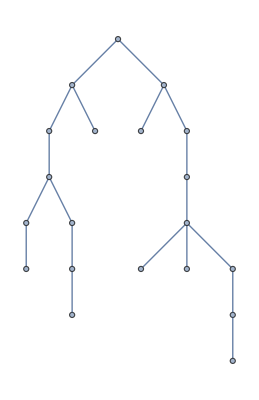

```mathematica
Graph[Map[{#[[1]],#[[2]]}&,mstMMA]]
```

```mathematica
(mstC=Map[MSTBaseShift[#,1]&,Import["iris.20.2.MST","Table"]]//Sort)//TableForm
```

1 | 5 | 0.141421
1 | 8 | 0.141421
1 | 18 | 0.
2 | 13 | 0.1
3 | 4 | 0.141421
3 | 10 | 0.223607
4 | 9 | 0.282843
5 | 20 | 0.223607
6 | 11 | 0.2
6 | 17 | 0.
6 | 19 | 0.316228
7 | 3 | 0.223607
8 | 12 | 0.2
9 | 14 | 0.141421
10 | 2 | 0.1
12 | 7 | 0.2
15 | 16 | 0.412311
19 | 15 | 0.223607
20 | 6 | 0.316228

```mathematica
Map[#[[3]]&,mstC]//Tr
```

3.58772

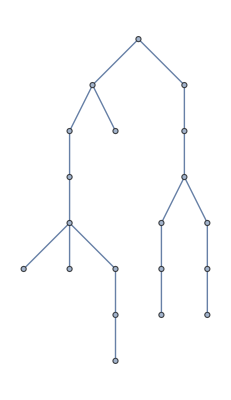

```mathematica
Graph[Map[{#[[1]],#[[2]]}&,mstC]]
```

同じ距離の異なるエッジがあった場合、どれを先に採用するかで結果が異なる。

## Performance

```mathematica
mstD[dmat_]:=Module[{pairdistS,seqMax,nodeClasses,head,headID,headClass,minClass,maxClass,maxClassMate,out,h,n},seqMax=Length[dmat];
pairdistS=Select[Sort[Flatten[MapIndexed[{#2,#1}&,dmat,{2}],1],#1[[2]]<#2[[2]]&],#[[1,1]]≠#[[1,2]]&];
nodeClasses=Range[seqMax];
(*recursive*)out=Reap[Sow[{},h];
Sow[nodeClasses,n];
While[Length[Union[nodeClasses]]≠1,({head,pairdistS}=shift[pairdistS];
headID=head[[1]];
headClass=nodeClasses[[headID]];
minClass=Min[headClass];
maxClass=Max[headClass];
maxClassMate=Flatten[Position[nodeClasses,maxClass]];
If[Length[Union[headClass]]==2,Sow[head,h];
nodeClasses[[headID[[1]]]]=minClass;
nodeClasses[[headID[[2]]]]=minClass;
nodeClasses[[maxClassMate]]=minClass;
Sow[nodeClasses,n];];
(*Print[pairdistS//Length,nodeClasses,head]*);)];
];
out[[2]]];
```

```mathematica
rl=Table[RandomReal[],{400},{2}];
```

```mathematica
rd=Outer[EuclideanDistance,rl,rl,1];
```

```mathematica
Timing[MSTdmat[rd];]
```

{7.85565,Null}

```mathematica
Timing[mstD[rd];]
```

{10.82835,Null}

```mathematica
rl=Table[RandomReal[],{10},{2}];
```

```mathematica
rd=Outer[EuclideanDistance,rl,rl,1];
```

```mathematica
sol1=MSTdmat[rd];
```

```mathematica
sol2=mstD[rd];
```

```mathematica
sol2//Length
```

2

```mathematica
sol1[[2]]
```

12

```mathematica
sol2[[2]]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,1,9,10},{1,2,3,4,5,6,7,1,9,3},{1,2,3,4,5,6,7,1,4,3},{1,2,3,4,5,3,7,1,4,3},{1,2,3,4,5,3,1,1,4,3},{1,2,3,1,5,3,1,1,1,3},{1,2,1,1,5,1,1,1,1,1},{1,1,1,1,5,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

```mathematica
g=WeightedAdjacencyGraph[rd];
```

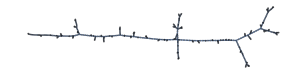

```mathematica
fg=FindSpanningTree[g,Method->"Kruskal"]
```

```mathematica
fg//EdgeList
```

{1<->263,1<->346,2<->164,2<->334,3<->65,3<->95,3<->121,4<->103,4<->236,5<->15,6<->74,6<->194,7<->118,7<->134,8<->13,8<->397,9<->31,9<->275,10<->199,10<->276,10<->349,11<->108,11<->120,11<->319,12<->44,12<->53,12<->383,13<->320,13<->321,14<->18,14<->377,15<->294,16<->123,16<->185,16<->215,17<->258,17<->379,18<->270,19<->172,19<->362,20<->68,20<->74,20<->237,21<->175,21<->332,21<->350,22<->92,22<->368,23<->52,23<->250,24<->193,25<->66,25<->315,26<->163,26<->274,27<->150,27<->260,27<->302,28<->338,29<->178,30<->227,30<->265,31<->261,31<->366,31<->376,32<->43,32<->397,33<->52,33<->300,34<->48,34<->157,34<->267,35<->329,36<->72,37<->66,37<->126,37<->303,38<->69,38<->125,39<->324,40<->154,40<->266,41<->154,41<->191,42<->56,42<->122,43<->59,43<->344,44<->239,45<->259,46<->285,47<->117,47<->254,47<->287,48<->245,49<->367,49<->380,50<->249,50<->281,50<->286,51<->225,51<->336,52<->72,53<->98,53<->146,54<->295,54<->382,55<->120,55<->193,56<->99,57<->166,57<->313,58<->226,60<->252,60<->393,61<->141,61<->189,62<->111,62<->205,63<->380,63<->398,64<->183,65<->331,65<->365,66<->288,67<->173,67<->329,68<->93,68<->252,69<->70,70<->83,71<->134,73<->155,73<->400,75<->260,76<->111,77<->156,77<->284,78<->162,78<->177,79<->199,79<->222,80<->298,80<->353,81<->369,81<->382,82<->109,82<->192,82<->311,83<->101,84<->308,84<->351,85<->132,86<->152,86<->264,87<->124,88<->162,88<->207,89<->326,89<->386,89<->398,90<->222,91<->327,92<->148,93<->149,94<->225,94<->232,95<->341,96<->156,96<->236,97<->184,97<->238,97<->306,98<->371,99<->149,100<->203,100<->243,101<->109,101<->307,102<->176,102<->368,103<->395,104<->144,104<->272,105<->292,106<->138,106<->360,107<->167,107<->346,108<->119,108<->356,110<->126,110<->244,111<->391,112<->166,112<->241,113<->184,114<->129,114<->398,115<->247,115<->260,116<->143,116<->364,116<->383,117<->324,118<->151,118<->253,120<->255,122<->159,122<->221,123<->160,123<->251,124<->276,125<->138,127<->186,127<->256,128<->288,130<->270,131<->220,131<->256,132<->241,133<->389,135<->248,136<->285,136<->286,137<->228,137<->336,138<->318,139<->305,140<->257,141<->395,142<->183,142<->359,143<->309,143<->387,144<->187,145<->214,146<->171,146<->321,147<->225,147<->343,148<->369,149<->170,150<->319,151<->231,151<->396,152<->230,153<->208,153<->296,153<->348,154<->387,158<->259,158<->325,159<->345,160<->399,161<->167,161<->261,162<->274,163<->184,164<->224,165<->269,165<->370,168<->292,168<->363,169<->383,170<->279,170<->342,172<->341,173<->211,174<->362,176<->312,178<->391,179<->196,180<->214,180<->309,181<->196,182<->361,183<->235,185<->211,186<->255,187<->234,187<->293,188<->202,188<->229,189<->197,190<->262,190<->313,190<->389,194<->277,195<->293,195<->328,195<->353,196<->273,197<->370,198<->283,198<->317,198<->344,200<->212,200<->350,201<->336,202<->345,203<->314,204<->310,205<->232,206<->251,206<->320,207<->326,208<->334,209<->279,209<->375,210<->216,210<->246,212<->308,213<->234,213<->257,215<->258,215<->377,216<->303,216<->390,217<->379,217<->392,218<->289,218<->330,219<->247,219<->312,220<->287,223<->273,226<->314,227<->231,228<->248,230<->283,230<->354,231<->373,233<->302,238<->384,240<->336,241<->337,242<->316,243<->374,244<->290,245<->250,245<->339,245<->349,247<->357,248<->316,248<->382,253<->282,256<->339,260<->378,262<->280,263<->351,264<->315,266<->272,267<->365,268<->396,269<->277,271<->299,272<->278,273<->295,274<->292,275<->323,275<->392,277<->355,280<->322,281<->282,284<->374,286<->385,289<->326,291<->307,291<->334,294<->363,296<->367,297<->309,298<->356,299<->323,301<->351,304<->358,305<->357,306<->343,310<->395,317<->388,322<->324,325<->351,325<->361,327<->328,330<->338,333<->388,335<->345,335<->348,340<->345,341<->394,347<->385,352<->381,352<->394,358<->399,359<->368,369<->372,373<->392,385<->400}

```mathematica
?*gWeight*
```

RowBox[{"WeightedAdjacencyGraph", "[", StyleBox["wmat", "TI"], "]"}] 重み付き隣接行列 StyleBox["wmat", "TI"] を持つグラフを与える．
RowBox[{"WeightedAdjacencyGraph", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["wmat", "TI"]}], "]"}] 頂点 SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]]，重み付き隣接行列 StyleBox["wmat", "TI"] のグラフを与える．